```mathematica
f = a*Exp[-t/t0]
```

a ⅇ^(-t/t0)

```mathematica
Integrate[f,t]
```

-a ⅇ^(-t/t0) t0

```mathematica
func = a*t0*(1-Exp[-t/t0])*HeavisideTheta[1/fs - t]*HeavisideTheta[t] +a*t0*Exp[-t/t0]*(Exp[1/(fs*t0)] - 1)*HeavisideTheta[t - 1/fs]
```

a (1-ⅇ^(-t/t0)) t0 HeavisideTheta[1/fs-t] HeavisideTheta[t]+a ⅇ^(-t/t0) (-1+ⅇ^(1/(fs t0))) t0 HeavisideTheta[-1/fs+t]

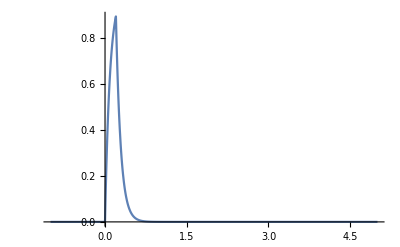

11.236

```mathematica
Plot[{func /. {t0 -> 0.089, fs -> 5, a -> 1/0.089}},{t,-1,5},PlotRange->All]
```

```mathematica
{{□}, {□}}
```